```mathematica
SecantMWI[x0_,x1_,n_,f_]:=
Module[{xk,xk1,xk2},xk=N[x0];xk1=N[x1];
i=0;
Output={};
While[i<n,
xk2=(xk*f[xk1]-xk1*f[xk])/(f[xk1]-f[xk]);
interval="["<>ToString[NumberForm[xk,12]]<>","<>ToString[NumberForm[xk1,12]]<>"]";
xk=xk1;xk1=xk2;
i++;
Output=Append[Output,{i,interval,xk2,f[xk2]}];];
Print[NumberForm[TableForm[Output,TableHeadings->{None,{"i","Interval","xi","f[xi]"}}],8]];
Print["Root after ",n," iterations = ",NumberForm[xk2,8]];
Print["Function value at approximate root, f[xi] = ",NumberForm[f[xk2],8]];];
Question 1
f[x_]:=x^3-5x+1;
SecantMWI[0,1,6,f]
```

i | Interval | xi | f[xi]
1 | [0.,1.] | 0.25 | -0.234375
2 | [1.,0.25] | 0.18644068 | 0.074277312
3 | [0.25,0.186440677966] | 0.20173626 | -0.00047111617
4 | [0.186440677966,0.201736256179] | 0.20163985 | -8.642293×10^-7
5 | [0.201736256179,0.201639852891] | 0.20163968 | 1.0352719×10^-11
6 | [0.201639852891,0.201639675721] | 0.20163968 | -2.220446×10^-16

Root after 6 iterations = 0.20163968

Function value at approximate root, f[xi] = -2.220446×10^-16

```mathematica
Question 2
f[x_]:=Cos[x]-x*Exp[x];
SecantMWI[0,1,8,f]
```

i | Interval | xi | f[xi]
1 | [0.,1.] | 0.31466534 | 0.51987117
2 | [1.,0.314665337801] | 0.44672814 | 0.20354478
3 | [0.314665337801,0.446728144591] | 0.53170586 | -0.042931093
4 | [0.446728144591,0.531705860645] | 0.51690447 | 0.0025927631
5 | [0.531705860645,0.516904467567] | 0.51774747 | 0.000030111941
6 | [0.516904467567,0.517747465271] | 0.51775737 | -2.1513165×10^-8
7 | [0.517747465271,0.517757370754] | 0.51775736 | 1.7807977×10^-13
8 | [0.517757370754,0.517757363682] | 0.51775736 | -3.3306691×10^-16

Root after 8 iterations = 0.51775736

Function value at approximate root, f[xi] = -3.3306691×10^-16

```mathematica
Question 3
f[x_]:=x^4-3*x^2+x-10;
SecantMWI[2,3,7,f]
```

i | Interval | xi | f[xi]
1 | [2.,3.] | 2.0784314 | -2.2198625
2 | [3.,2.07843137255] | 2.119995 | -1.1637008
3 | [2.07843137255,2.11999499205] | 2.1657906 | 0.096032538
4 | [2.11999499205,2.16579064846] | 2.1622995 | -0.0036507762
5 | [2.16579064846,2.16229953415] | 2.1624274 | -0.000010786812
6 | [2.16229953415,2.16242739183] | 2.1624278 | 1.2174048×10^-9
7 | [2.16242739183,2.16242777073] | 2.1624278 | 1.7763568×10^-15

Root after 7 iterations = 2.1624278

Function value at approximate root, f[xi] = 1.7763568×10^-15

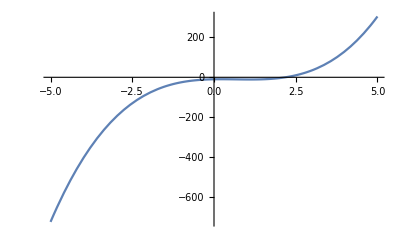

```mathematica
Question 4
f[x_]:=4*x^3-8*x^2+3*x-10;
Plot[f[x],{x,-5,5}]
```

```mathematica
SecantMWI[0,2,8,f]
```

i | Interval | xi | f[xi]
1 | [0.,2.] | 3.3333333 | 59.259259
2 | [2.,3.33333333333] | 2.0843091 | -2.2820009
3 | [3.33333333333,2.08430913349] | 2.130624 | -1.2362271
4 | [2.08430913349,2.13062398529] | 2.1853736 | 0.097391729
5 | [2.13062398529,2.18537356592] | 2.1813753 | -0.0036503741
6 | [2.18537356592,2.18137530485] | 2.1815198 | -0.000010127519
7 | [2.18137530485,2.18151975105] | 2.1815202 | 1.0581083×10^-9
8 | [2.18151975105,2.18152015292] | 2.1815202 | 1.7763568×10^-15

Root after 8 iterations = 2.1815202

Function value at approximate root, f[xi] = 1.7763568×10^-15